1. Вынужденные колебания малой частоты (ω₀ >> ω)

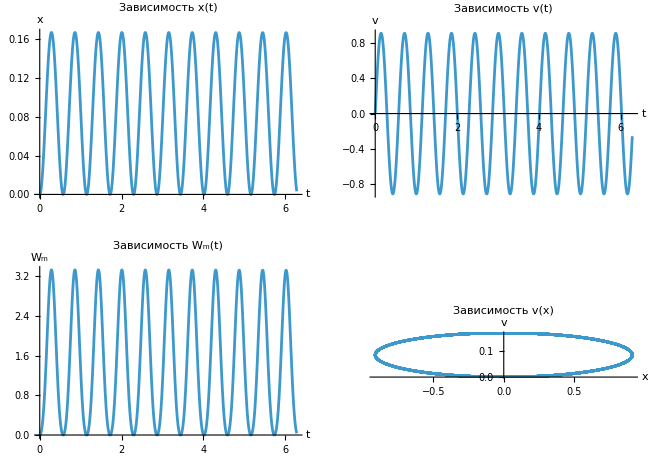

2. Вынужденные колебания большой частоты (ω₀ << ω)

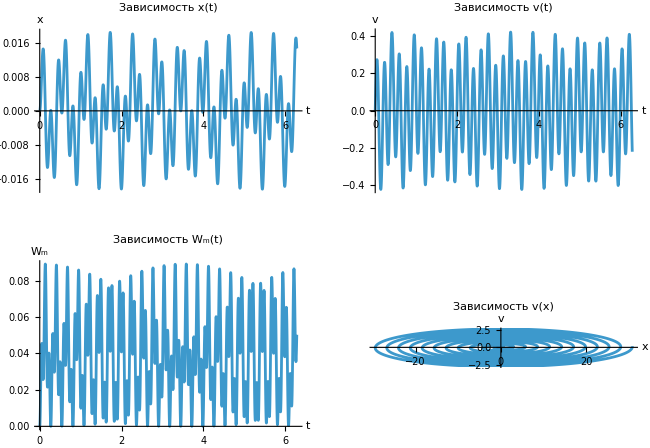

3. Резонанс (ω₀ ≈ ω)

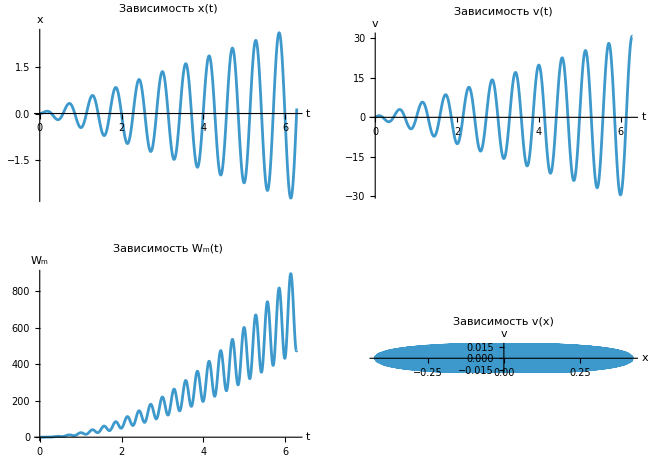

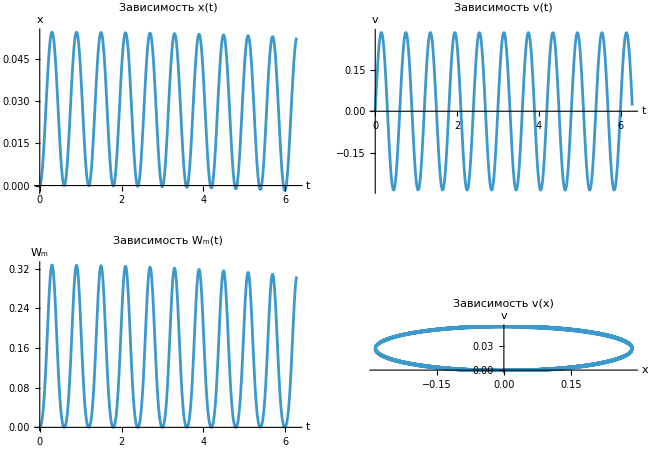

```mathematica
ClearAll["Global`*"];

Fm=10;
m=1;
k=120;
ω0=Sqrt[k/m];
ω={ω0 10^-3,ω0 1.01,ω0*10^0.5};
x0=0;
v0=0;

(*Решения дифференциальных уравнений*)
sol1=DSolve[{x''[t] m+k x[t]-Fm Cos[ω[[1]] t]==0,x[0]==x0,x'[0]==v0},x[t],t];
sol2=DSolve[{x''[t] m+k x[t]-Fm Cos[ω[[2]] t]==0,x[0]==0,x'[0]==0},x[t],t];
sol3=DSolve[{x''[t] m+k x[t]-Fm Cos[ω[[3]] t]==0,x[0]==0,x'[0]==0},x[t],t];

sol4=DSolve[{x''[t] m+k x[t]-Fm==0,x[0]==x0,x'[0]==v0},x[t],t];

(*Определение функций*)
x1[t_]=x[t]/. sol1[[1]];
x2[t_]=x[t]/. sol2[[1]];
x3[t_]=x[t]/. sol3[[1]];

x4[t_]=x[t]/. sol4[[1]];


v1[t_]=D[x1[t],t];
v2[t_]=D[x2[t],t];
v3[t_]=D[x3[t],t];

Wm1[t_]=m (x1'[t])^2/2+k (x1[t])^2;
Wm2[t_]=m (x2'[t])^2/2+k (x2[t])^2;
Wm3[t_]=m (x3'[t])^2/2+k (x3[t])^2;

Wm4[t_]=m (x4'[t])^2/2+k (x4[t])^2;

(*Первый случай-Вынужденные колебания малой частоты*)
Print[Style["1. Вынужденные колебания малой частоты (ω₀ >> ω)",FontSize->18,Bold]];

GraphicsGrid[{{Plot[x1[t],{t,0,2 Pi},AxesLabel->{t,x},PlotLabel->Style["Зависимость x(t)",FontSize->14],ImageSize->300],Plot[x1'[t],{t,0,2 Pi},AxesLabel->{t,"v"},PlotLabel->Style["Зависимость v(t)",FontSize->14],ImageSize->300]},{Plot[Wm1[t],{t,0,2 Pi},AxesLabel->{t,"Wₘ"},PlotLabel->Style["Зависимость Wₘ(t)",FontSize->14],ImageSize->300],ParametricPlot[{x1'[t],x1[t]},{t,0,2 Pi},AxesLabel->{x,v},PlotLabel->Style["Зависимость v(x)",FontSize->14],ImageSize->300]}},ImageSize->650]

(*Действие постоянной силы*)
(*
Print[Style["Действие постоянной силы (для сравнения)",FontSize->18,Bold]];

GraphicsGrid[{{Plot[x4[t],{t,0,2 Pi},AxesLabel->{t,x},PlotLabel->Style["Зависимость x(t)",FontSize->14],ImageSize->300],Plot[x4'[t],{t,0,2 Pi},AxesLabel->{t,"v"},PlotLabel->Style["Зависимость v(t)",FontSize->14],ImageSize->300]},{Plot[Wm4[t],{t,0,2 Pi},AxesLabel->{t,"Wₘ"},PlotLabel->Style["Зависимость Wₘ(t)",FontSize->14],ImageSize->300],ParametricPlot[{x4'[t],x4[t]},{t,0,2 Pi},AxesLabel->{v,x},PlotLabel->Style["Зависимость v(x)",FontSize->14],ImageSize->300]}},ImageSize->650]
*)
(*Второй случай-Вынужденные колебания большой частоты*)
Print[Style["2. Вынужденные колебания большой частоты (ω₀ << ω)",FontSize->18,Bold]];

GraphicsGrid[{{Plot[x3[t],{t,0,2 Pi},AxesLabel->{t,x},PlotLabel->Style["Зависимость x(t)",FontSize->14],ImageSize->300],Plot[x3'[t],{t,0,2 Pi},AxesLabel->{t,"v"},PlotLabel->Style["Зависимость v(t)",FontSize->14],ImageSize->300]},{Plot[Wm3[t],{t,0,2 Pi},AxesLabel->{t,"Wₘ"},PlotLabel->Style["Зависимость Wₘ(t)",FontSize->14],ImageSize->300],ParametricPlot[{x2'[t],x2[t]},{t,0,2 Pi},AxesLabel->{x,v},PlotLabel->Style["Зависимость v(x)",FontSize->14],ImageSize->300]}},ImageSize->650]

(*Третий случай-Резонанс*)
Print[Style["3. Резонанс (ω₀ ≈ ω)",FontSize->18,Bold]];

GraphicsGrid[{
{
Plot[x2[t],{t,0,2 Pi},AxesLabel->{t,x},PlotLabel->Style["Зависимость x(t)",FontSize->14],ImageSize->300],Plot[x2'[t],{t,0,2 Pi},AxesLabel->{t,"v"},PlotLabel->Style["Зависимость v(t)",FontSize->14],ImageSize->300]
},
{
Plot[Wm2[t],{t,0,2 Pi},AxesLabel->{t,"Wₘ"},PlotLabel->Style["Зависимость Wₘ(t)",FontSize->14],ImageSize->300],ParametricPlot[{x3'[t],x3[t]},{t,0,2 Pi},AxesLabel->{x,v},PlotLabel->Style["Зависимость v(x)",FontSize->14],ImageSize->300]
}
},ImageSize->650]
```